```mathematica
voltageData={{0.,0.},{0.05,0.62},{0.19,1.97},{0.25,2.65},{0.33,3.34},{0.66,6.72},{1.29,12.92},{1.93,19.33}}
```

{{0.,0.},{0.05,0.62},{0.19,1.97},{0.25,2.65},{0.33,3.34},{0.66,6.72},{1.29,12.92},{1.93,19.33}}

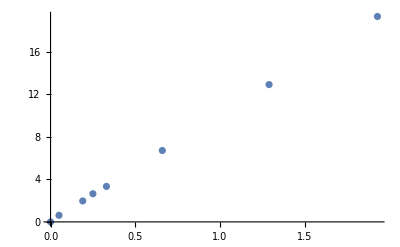

```mathematica
ListPlot[voltageData]
```

```mathematica
voltageFit=LinearModelFit[voltageData,x,x]
```

FittedModel[0.0849436+9.97244 x]

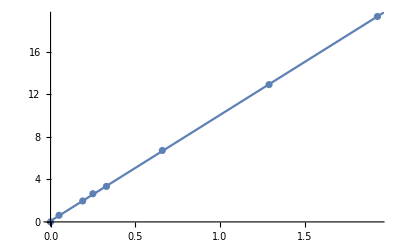

```mathematica
Show[ListPlot[voltageData],Plot[voltageFit[x],{x,0,2}]]
```

```mathematica
slope=9.97244;
```

## Periodicities

### 160K

```mathematica
dv160=500/28//N;
```

```mathematica
periodicities160={27*dv160,28*dv160,27*dv160}
```

{482.143,500.,482.143}

```mathematica
sigmas160={dv160,dv160,dv160}
```

{17.8571,17.8571,17.8571}

### 152K

```mathematica
dv152=500/28//N;
```

```mathematica
periodicities152={27*dv152,28*dv152,29*dv152}
```

{482.143,500.,517.857}

```mathematica
sigmas152={dv152,dv152,dv152}
```

{17.8571,17.8571,17.8571}

### 140K

```mathematica
dv140=200/28//N;
```

```mathematica
periodicities140={71*dv140}
```

{507.143}

```mathematica
sigmas140={2*dv140}
```

{14.2857}

### Totals

```mathematica
periodicities=Join[periodicities160,periodicities152,periodicities140]
```

{482.143,500.,482.143,482.143,500.,517.857,507.143}

```mathematica
sigmas=Join[sigmas160,sigmas152,sigmas140]
```

{17.8571,17.8571,17.8571,17.8571,17.8571,17.8571,14.2857}

```mathematica
avg=Mean[periodicities]
```

495.918

```mathematica
finalAvg=slope*avg
```

4945.52

## First Maximum Location

### 159K

```mathematica
dv159=100/28//N;
```

```mathematica
max159={196*dv159}
```

{700.}

```mathematica
sigmaMax159={4*dv159}
```

{14.2857}

### 160K

```mathematica
dv160=500/28//N;
```

```mathematica
max160={41*dv160}
```

{732.143}

```mathematica
sigmaMax160={dv160}
```

{17.8571}

### 140K(1)

```mathematica
dv140=100/28//N;
```

```mathematica
max140={191*dv140}
```

{682.143}

```mathematica
sigmaMax140={4*dv140}
```

{14.2857}

### 140K(2)

```mathematica
dv1402=200/28//N;
```

```mathematica
max1402={98*dv1402}
```

{700.}

```mathematica
sigmaMax1402={2*dv1402}
```

{14.2857}

### 152K

```mathematica
dv152=500/28//N;
```

```mathematica
max152={38*dv152}
```

{678.571}

```mathematica
sigmaMax152={dv152}
```

{17.8571}

### 154K

```mathematica
dv154=100/28//N;
```

```mathematica
max154={195*dv154}
```

{696.429}

```mathematica
sigmaMax154={4*dv154}
```

{14.2857}

### Total

```mathematica
max=Join[max159,max160,max140,max1402,max152,max154]
```

{700.,732.143,682.143,700.,678.571,696.429}

```mathematica
maxAvg=Mean[max]*slope
```

6962.9

```mathematica
6963-4946
```

2017

```mathematica
finalAvg
```

4945.52

```mathematica
Vc=maxAvg-finalAvg
```

2017.38

```mathematica
sigmaMax=Join[sigmaMax159,sigmaMax160,sigmaMax140,sigmaMax1402,sigmaMax152,sigmaMax154]
```

{14.2857,17.8571,14.2857,14.2857,17.8571,14.2857}

## Error

```mathematica
σp=Sqrt[Sum[(1/7)*sigmas⟦i⟧^2,{i,1,7}]]*slope/1000
```

0.17344

```mathematica
σVc=Sqrt[Sum[(1/6)*sigmaMax⟦i⟧^2,{i,1,6}]]*slope/1000
```

0.155246